```mathematica
Quit[]
```

# Calculations

```mathematica
<<FeynCalc`
```

FeynCalc 9.2.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

```mathematica
(*Ниже идет расчет гамма тау*)
```

```mathematica
Clear[H,cH,H2,H3,H4,H6,HT,λ,p1,p2,q2,q,m1,m2];
ScalarProduct[p1,p1]=m1^2;
ScalarProduct[p2,p2]=m2^2;
ScalarProduct[p1,p2]=(m1^2+m2^2-q2)/2;
q=p1-p2;
H =SpinorUBar[p2,m2].GA[μ].(1+GA[5]).SpinorU[p1, m1];
cH= ComplexConjugate[H]/.{μ->α,ν->β};
H2=H*cH;
H3=DiracSimplify[FermionSpinSum[H2]]/.{DiracTrace->TR};
H6=Simplify[Calc[H3]];
H4=Simplify[Calc[H3*(FV[q,μ]*FV[q,α]-q2*MT[μ,α])]];

HT:=λ*H4;
HT
```

4 λ (m1^4+m1^2 (q2-2 m2^2)+m2^4+m2^2 q2-2 q2^2)

```mathematica
m2=0;
m1=mtau;
HT
```

4 λ (mtau^4+mtau^2 q2-2 q2^2)

```mathematica
dΓ3π= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*(1/(8*π))*HT*Fq3π
```

(Fq3π Gf^2 λ (mtau^4+mtau^2 q2-2 q2^2))/(8 π mtau (2 Y+1))

Calculations

## Initial constants

```mathematica
Y=1/2;
Gf=1.166*10^(-5);
dm232=1;
a1=1.07;
Fm2320=1/(3*π);
mπ=0.13957061;
fπ=0.1304;
mρ=0.7665;
fρ=0.216;
ma1=1.230;
fa1=0.238;
SetAttributes[V,Orderless];
V["c","b"]=0.0411;V["c","s"]=0.974;V["c","d"]=0.225;
V["u","b"]=0.00357;V["u","s"]=0.225;V["u","d"]=0.974;
```

## Initial Tau lepton calculations for constants 3pi 5pi

```mathematica
(*τ->3π*)
Clear[H,cH,H2,H3,H4,H6,HT,λ,p1,p2,q2,q,m1,m2];
ScalarProduct[p1,p1]=m1^2;
ScalarProduct[p2,p2]=m2^2;
ScalarProduct[p1,p2]=(m1^2+m2^2-q2)/2;
q=p1-p2;
H =SpinorUBar[p2,m2].GA[μ].(1+GA[5]).SpinorU[p1, m1];
cH= ComplexConjugate[H]/.{μ->α,ν->β};
H2=H*cH;
H3=DiracSimplify[FermionSpinSum[H2]]/.{DiracTrace->TR};
H6=Simplify[Calc[H3]];
H4=Simplify[Calc[H3*(FV[q,μ]*FV[q,α]-q2*MT[μ,α])]];
λ:=√(1-((m2+√q2)/m1)^2)*√(1-((m2-√q2)/m1)^2);
HT:=λ*H4;
HT;
Fq3π1=2.93*10^-5*((q2-9*mπ^2)/q2)^4*(1+190q2)/(((q2-1.06)^2+0.48)^2);
Fq3π=(0.000058592966004157997*(-0.17640000000000003+q2)^4*(1+1.510651725804281*^-105*q2+189.45911486214024*q2^2))/((0.48273650253772327+(-1.0373349238887504+q2)^2)^2*q2^4)/2;
dΓ3π= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*(1/(8*π))*HT*Fq3π;
dΓ3π1= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*(1/(8*π))*HT*Fq3π1;
(*Decay to 3π*)
m1=1.776;
m2=0;
h=6.5*10^-25;τ=290*10^-15;
Γτ=h/τ;
Const3π=1;
Γ3π=NIntegrate[dΓ3π, {q2,9mπ^2,(m1-m2)^2}];
Clear[Const3π];
Br=Γ3π/Γτ;
BrNorm=0.0903;
Const3π =BrNorm/Br
Γ3π=Const3π*NIntegrate[dΓ3π, {q2,9mπ^2,(m1-m2)^2}];
Br=Γ3π/Γτ;
Error=Br/BrNorm
```

1.34154

1.

```mathematica
(*Считаем константу для распада тау лептона в пять пи мезонов*)
Clear[Br,BrNorm];
Fq5π=32*((q2-25*mπ^2)/q2)^10*(1-1.65*q2+0.69q2^2)/(((q2+2.21)^2-4.69)^3);
dΓ5π= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*(1/(8*π))*HT*Fq5π;
Γ5π=NIntegrate[dΓ5π, {q2,25mπ^2,(m1-m2)^2}];
Br=Γ5π/Γτ;
BrNorm=0.000769;
Const5π=BrNorm/Br
Γ5π=Const5π*NIntegrate[dΓ5π, {q2,25mπ^2,(m1-m2)^2}];
Br=Γ5π/Γτ;
Error=Br/BrNorm
```

0.864687

1.

```mathematica
Clear[Br,BrNorm];
Fq2π=(0.0013516183448589506*(1+0.6384423540947195*q2)*(-0.07840000000000001+q2)^2)/((0.013064170424296547+(-0.5686550420645691+q2)^2)*q2^2);
dΓ2π= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*(1/(8*π))*HT*Fq2π;
Γ2π=NIntegrate[dΓ2π, {q2,4mπ^2,(m1-m2)^2}];
Br=Γ2π/Γτ;
BrNorm=0.2549;
Const2π=BrNorm/Br
Γ2π=Const2π*NIntegrate[dΓ2π, {q2,4mπ^2,(m1-m2)^2}];
Br=Γ2π/Γτ;
Error=Br/BrNorm
```

1.25599

1.

```mathematica
Clear[Br,BrNorm];
Fq4π=(0.00017983715820604627*(-0.31360000000000005+q2)*(1+5.074780646730226*q2+8.631754238222705*q2^2))/((0.6162735882355033+(-1.834698151162789+q2)^2)^2*q2);
dΓ4π= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*(1/(8*π))*HT*Fq4π;
Γ4π=NIntegrate[dΓ4π, {q2,16mπ^2,(m1-m2)^2}];
Br=Γ4π/Γτ
BrNorm=0.0462;
Const4π=BrNorm/Br
Γ4π=Const4π*NIntegrate[dΓ4π, {q2,16mπ^2,(m1-m2)^2}];
Br=Γ4π/Γτ;
Error=Br/BrNorm
```

0.0374275

1.23439

1.

## Clear

```mathematica
Clear[Fq3π1,Fq2π,Fq3π,Fq4π,Fq5π,Γ2π,Γ3π,Γ4π,Γ5π,dΓ2π,dΓ3π,dΓ3π1,dΓ4π,dΓ5π,H,cH,H2,H3,H4,H6,HT,λ,p1,p2,q2,q,m1,m2];
ClearScalarProducts;
```

## Init

```mathematica
Clear[H,cH,H2,H3,H4,H6,HT,λ,p1,p2,m232,q,m1,m2,m3,m4, Fq3π,Fq5π,Br,f1,f2,g1,g2];
ScalarProduct[p11,p11]=m1^2;
ScalarProduct[p22,p22]=m2^2;
ScalarProduct[p11,p22]=(m1^2+m2^2-m232)/2;
SetMandelstam[m232,m132,m122,p1,-p2,-pe,-ke,m1,m2,0,0];
qq=p11-p22;
q=p1-p2;
sigma=I*(GA[μ].GA[ν]-GA[ν].GA[μ])/2;
H =SpinorUBar[p22,m2].(GA[μ]*f1+I*sigma*FV[qq,ν]*f2/m1).SpinorU[p11, m1]-SpinorUBar[p22,m2].(GA[μ]*g1+ⅈ*sigma*FV[qq,ν]*g2/m1).GA[5].SpinorU[p11, m1];
HH=SpinorUBar[p2,m2].(GA[μ]*f1+I*sigma*FV[q,ν]*f2/m1).SpinorU[p1, m1]-SpinorUBar[p2,m2].(GA[μ]*g1+ⅈ*sigma*FV[q,ν]*g2/m1).GA[5].SpinorU[p1, m1];
cH= ComplexConjugate[H]/.{μ->α,ν->β};
cHH= ComplexConjugate[HH]/.{μ->α,ν->β};
H2=H*cH;
HH2=HH*cHH;
HH3=DiracSimplify[FermionSpinSum[HH2]]/.{DiracTrace->TR};
H3=DiracSimplify[FermionSpinSum[H2]]/.{DiracTrace->TR};
H6=Simplify[Calc[H3]];
H4=Simplify[Calc[H3*(FV[qq,μ]*FV[qq,α]-m232*MT[μ,α])]];
λ:=√(1-((m2+√m232)/m1)^2)*√(1-((m2-√m232)/m1)^2);
HT:=λ*H4;
(*T=Transversal*)
HL:=λ*Simplify[Calc[H3*(FV[qq,μ]*FV[qq,α])]];
(*L=Longitudinal*)
L=SpinorUBar[pe].GA[μ].(1+GA[5]).SpinorV[ke];
cL=ComplexConjugate[L]/.{μ->α};
L2=FermionSpinSum[L*cL]/.{DiracTrace->TR};
M2=Simplify[1/2*Gf^2*Calc[HH3*L2]];
M3=M2//.m132->m1^2+m2^2-m122-m232;
E2ZV= (m122-m2^2 +m3^2)/(2*Sqrt[m122]) (*  E2^*  *);
E3ZV= (m1^2-m122-m4^2)/(2*Sqrt[m122])  (*  E3^*  *);
m23min=(E2ZV+E3ZV)^2-(Sqrt[E2ZV^2-m3^2]+Sqrt[E3ZV^2-m4^2])^2;
m23max=Simplify[Calc[(E2ZV+E3ZV)^2-(Sqrt[E2ZV^2-m3^2]-Sqrt[E3ZV^2-m4^2])^2]];
m12min=m2^2;
m12max=m1^2;
```

```mathematica
qqqq=H4;
wwww=HL/λ;
```

```mathematica
StringReplace[StringReplace[ToString[Simplify[m1^2 2 qqqq,m1==(Mplus+Mminus)/2&&m2==(Mplus-Mminus)/2],TeXForm],{"\\text{f1}"->"f_1","\\text{f2}"->"f_2","\\text{g1}"->"g_1","\\text{g2}"->"g_2","\\text{Mplus}"->"M_{+}","\\text{Mminus}"->"M_{-}","\\text{m232}"->"q^2","\\left"->"","\\right"->""}],{"q^2^2"->"q^4"}]
```

f_1^2 (M_{-}+M_{+})^2 (-2 q^4+2 q^2 M_{-}^2-q^2 M_{+}^2+M_{-}^2 M_{+}^2)+12 f_1 f_2 q^2 M_{+} (q^2-M_{-}^2) (M_{-}+M_{+})-4 f_2^2 q^2 (q^4-q^2 M_{-}^2+2 q^2 M_{+}^2-2 M_{-}^2 M_{+}^2)+g_1^2 (M_{-}+M_{+})^2 (-2 q^4-q^2 M_{-}^2+2 q^2 M_{+}^2+M_{-}^2 M_{+}^2)+12 g_1 g_2 q^2 M_{-} (M_{+}^2-q^2) (M_{-}+M_{+})-4 g_2^2 q^2 (q^4+2 q^2 M_{-}^2-q^2 M_{+}^2-2 M_{-}^2 M_{+}^2)

```mathematica
StringReplace[StringReplace[ToString[Simplify[m1^2 2  wwww,m1==(Mplus+Mminus)/2&&m2==(Mplus-Mminus)/2],TeXForm],{"\\text{f1}"->"f_1","\\text{f2}"->"f_2","\\text{g1}"->"g_1","\\text{g2}"->"g_2","\\text{Mplus}"->"M_{+}","\\text{Mminus}"->"M_{-}","\\text{m232}"->"q^2","\\left"->"","\\right"->""}],{"q^2^2"->"q^4"}]
```

(M_{-}+M_{+})^2 (f_1^2 M_{-}^2 (M_{+}^2-q^2)+g_1^2 M_{+}^2 (M_{-}^2-q^2))

```mathematica
dΓl:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*dm232 /(2*π)*(1/(8*π))*Vckm^2*HT*Fm2320
dΓl1:=(1/2)*(1/(2*π)^3)*(1/(32*m1^3))*Vckm^2*M3;

ΓV:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*fP^2*(1/(8*π))*Vckm^2*HT;
(*ΓV - распад в векторыные мезоны*)
ΓP:=(Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*fP^2*(1/(8*π))*Vckm^2*HL;
(*ΓP - распад в псевдоскалярные мезоны*)
Fq2π:=Const2π*(0.0013516183448589506*(1+0.6384423540947195*m232)*(-0.07840000000000001+m232)^2)/((0.013064170424296547+(-0.5686550420645691+m232)^2)*m232^2);
Fq3π:=Const3π*2.93*10^-5*((m232-9*mπ^2)/m232)^4*(1+190m232)/(((m232-1.06)^2+0.48)^2);
Fq4π:=Const4π* (0.00017983715820604627*(-0.31360000000000005+m232)*(1+5.074780646730226*m232+8.631754238222705*m232^2))/((0.6162735882355033+(-1.834698151162789+m232)^2)^2*m232);
Fq5π:=Const5π*32*((m232-25*mπ^2)/m232)^10*(1-1.65*m232+0.69m232^2)/(((m232+2.21)^2-4.69)^3);

dΓ2π:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*Fq2π;
dΓ3π:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*Fq3π;
dΓ4π:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*Fq4π;
dΓ5π:=  (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*Fq5π;
```

## File

```mathematica
SetDirectory[NotebookDirectory[]];
<<"wang_data.m";
decays={#["in"],#["out"]}&/@Normal[DeleteDuplicates[dsFF[All,{"in","out"}]]];
Clear[$FF];
$FF[data_]:=Module[{},Switch[data["func"],"FF",Return[data["F0"]/(1-m232/data["mFit"]^2+data["delta"] (m232/data["mFit"]^2)^2)];,"GG",Return[data["F0"]/(1+m232/data["mFit"]^2+data["delta"] (m232/data["mFit"]^2)^2)];];];
(*Clear[cS,cA];*)
Clear[FF];
FF[query_]:=Module[{$res},$res=dsFF[query];
Return[cS $FF[$res[1]]+cA $FF[$res[2]]]];
```

## Test

```mathematica
in="\\Omega_{cc}^{+}";
out="\\Omega_{c}^{0}";
testresult={};
AppendTo[testresult,{"in","out","l nul" ,"pi","rho","3 pi","a1","5 pi"}];
Clear[m1,m2,quark1,quark2,f1,f2,g1,g2,Vckm,cS,cA];
m1=dsParticles[in]["mass"]; m2=dsParticles[out]["mass"];
cA=cA1[out,in];cS=cS1[out,in];
f1=FF[Select[#in==in&&#out==out&&#f=="f1"&]];
f2=FF[Select[#in==in&&#out==out&&#f=="f2"&]];
g1=FF[Select[#in==in&&#out==out&&#f=="g1"&]];
g2=FF[Select[#in==in&&#out==out&&#f=="g2"&]];
quark1=Characters[Quarks[in]];
quark2=Characters[Quarks[out]];
Vckm1=First[(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]])];
quarkrazn=(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]]);
Vckm2=-quarkrazn+Vckm1;
Vckm=V[Vckm1,Vckm2];
m3=0; m4=0;
Γl1=NIntegrate[dΓl, {m232,0,(m1-m2)^2}];
Γl2=NIntegrate[dΓl1,{m122,m12min,m12max},{m232,m23min,m23max}];
Γl0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\nu"]&]][[1]]["width"];
Brl=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\nu"]&]][[1]]["br"];
fullΓ=Γl0/Brl;
Hρ=HT/.{m232-> mρ^2};
Γρ=(Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*fρ^2*(1/(8*π))*a1*Vckm^2*Hρ;
Hπ=HL/.{m232-> mπ^2};
Γπ=(Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*fπ^2*(1/(8*π))*a1*Vckm^2*Hπ;
Γρ0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\rho"]&]][[1]]["width"];
Γπ0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\pi"]&]][[1]]["width"];
Γa1=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\a_1"]&]][[1]]["width"];
Γ3π=NIntegrate[dΓ3π, {m232,9mπ^2,(m1-m2)^2}];
Γ5π=NIntegrate[dΓ5π, {m232,25mπ^2,(m1-m2)^2}];
AppendTo[testresult,{in,out,Floor[Chop[Γl1/fullΓ],-0.00001]*100,Floor[Chop[Γπ/fullΓ],-0.00001]*100,Floor[Chop[Γρ/fullΓ],-0.00001]*100, Floor[Chop[Γ3π/fullΓ],-0.00001]*100,Floor[Chop[Γa1/fullΓ],-0.00001]*100,Floor[Chop[Γ5π/fullΓ],-0.000001]*100}];
testresult
```

(in | out | l nul | pi | rho | 3 pi | a1 | 5 pi
\Omega_{cc}^{+} | \Omega_{c}^{0} | 6.661 | 6.951 | 24.136 | 0.736 | 100 Floor[4.10494×10^11 Missing[PartAbsent,1][width],-0.00001] | 0.0003)

```mathematica
Γa1=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"a_{1}"]&]][[1]]["width"]
```

```mathematica
Missing["PartAbsent",1]
```

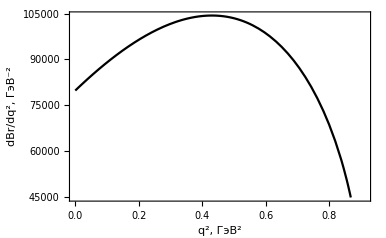

```mathematica
pic1 = Plot[dΓl*5*10^17,{m232,0,(m1-m2)^2},PlotStyle->Black,FrameLabel->{"q^2, (:0413:044d:0412)^2","dBr/dq^2, (:0413:044d:0412)^-2"}, Frame-> True ]
```

```mathematica
SetDirectory[NotebookDirectory[]];
tab=ReadList["m2_23.txt",{Number,Number,Number}];
tab=tab[[All,1;;2]];
```

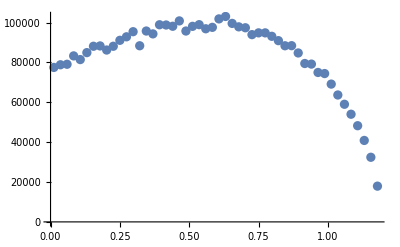

```mathematica
pic2=ListPlot[tab]
```

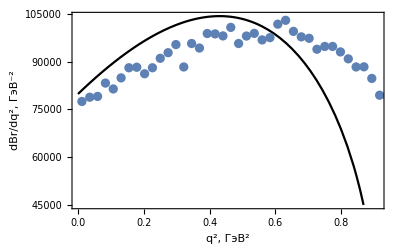

```mathematica
Show[pic1, pic2]
```

## Main calculation

```mathematica
result={};
AppendTo[result,{"in","out","l nul","pi" ,"rho","2 pi","3 pi","a1","4 pi","5 pi"}];
i=.0;
PrintTemporary[Dynamic[dec],"Завершено",Dynamic[Floor[i/36*100,-0.1]], "%" ];
Do[
{in,out}=dec;
i=i+1;
Clear[m1,m2,quark1,quark2,f1,f2,g1,g2,Vckm,cS,cA];
m1=dsParticles[in]["mass"]; m2=dsParticles[out]["mass"];
cA=cA1[out,in];cS=cS1[out,in];
f1=FF[Select[#in==in&&#out==out&&#f=="f1"&]];
f2=FF[Select[#in==in&&#out==out&&#f=="f2"&]];
g1=FF[Select[#in==in&&#out==out&&#f=="g1"&]];
g2=FF[Select[#in==in&&#out==out&&#f=="g2"&]];
quark1=Characters[Quarks[in]];
quark2=Characters[Quarks[out]];
Vckm1=First[(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]])];
quarkrazn=(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]]);
Vckm2=-quarkrazn+Vckm1;
Vckm=V[Vckm1,Vckm2];
m3=0; m4=0;
Γl1=NIntegrate[dΓl, {m232,0,(m1-m2)^2}];
Γl2=NIntegrate[dΓl1,{m122,m12min,m12max},{m232,m23min,m23max}];
Γl0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\nu"]&]][[1]]["width"];
Brl=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\nu"]&]][[1]]["br"];
fullΓ=Γl0/Brl;
Hρ=HT/.{m232-> mρ^2};
Γρ=(Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*fρ^2*(1/(8*π))*Vckm^2*Hρ;
Hπ=HL/.{m232-> mπ^2};
Γπ=(Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*fπ^2*(1/(8*π))*Vckm^2*Hπ;
Ha1=HT/.{m232-> ma1^2};
Γa1=(Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*fa1^2*(1/(8*π))*a1*Vckm^2*Ha1;
Γρ0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\rho"]&]][[1]]["width"];
Γπ0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\pi"]&]][[1]]["width"];
Γ2π=NIntegrate[dΓ2π, {m232,4mπ^2,(m1-m2)^2}];
Γ3π=NIntegrate[dΓ3π, {m232,9mπ^2,(m1-m2)^2}];
Γ4π=NIntegrate[dΓ4π, {m232,16mπ^2,(m1-m2)^2}];
Γ5π=NIntegrate[dΓ5π, {m232,25mπ^2,(m1-m2)^2}];
AppendTo[result,{in,out,Floor[Chop[Γl1/fullΓ],-0.000001]*100,Floor[Chop[Γπ/fullΓ],-0.0000000001]*100,Floor[Chop[Γρ/fullΓ],-0.00000001]*100,Floor[Chop[Γ2π/fullΓ],-0.0000001]*100,Floor[Chop[Γ3π/fullΓ],-0.0000001]*100,Re[Floor[Chop[Γa1/fullΓ],-0.0000001]*100],Floor[Chop[Γ4π/fullΓ],-0.0000001]*100,Floor[Chop[Γ5π/fullΓ],-0.0000001]*100}];
,{dec,decays}];
result
```

$Aborted

(in | out | l nul | pi | rho | 2 pi | 3 pi | a1 | 4 pi | 5 pi
\Xi_{cc}^{++} | \Lambda_{c}^{+} | 0.4936 | 0.377359 | 0.9932 | 0.8646 | 0.20393 | 0.49109 | 0.04814 | 0.00027
\Xi_{cc}^{++} | \Sigma_{c}^{+} | 0.4503 | 0.24423 | 1.04919 | 0.90497 | 0.18642 | 0. | 0.02255 | 0.00009
\Xi_{cc}^{++} | \Xi_{c}^{+} | 4.9858 | 6.4213 | 12.3268 | 10.171 | 0.98917 | 0. | 0.09019 | 0.00039
\Xi_{cc}^{++} | \Xi_{c}^{\prime+} | 5.975 | 4.65871 | 17.6055 | 14.255 | 1.31453 | 0. | 0.10158 | 0.00056
\Xi_{cc}^{+} | \Sigma_{c}^{0} | 0.2988 | 0.162432 | 0.69752 | 0.60138 | 0.12326 | 0. | 0.01483 | 0.00006
\Xi_{cc}^{+} | \Xi_{c}^{0} | 1.6513 | 2.12669 | 4.08255 | 3.36855 | 0.32761 | 0. | 0.02987 | 0.00013
\Xi_{cc}^{+} | \Xi_{c}^{\prime0} | 1.984 | 1.5506 | 5.85562 | 4.73854 | 0.43377 | 0. | 0.03345 | 0.00019
\Omega_{cc}^{+} | \Xi_{c}^{0} | 0.2079 | 0.238002 | 0.512133 | 0.42522 | 0.04921 | 0. | 0.00491 | 0.00002
\Omega_{cc}^{+} | \Xi_{c}^{\prime0} | 0.2492 | 0.172445 | 0.710986 | 0.58352 | 0.06489 | 0. | 0.0053 | 0.00003
\Omega_{cc}^{+} | \Omega_{c}^{0} | 6.6604 | 6.49593 | 22.5567 | 17.1055 | 0.73517 | 0. | 0.05073 | 0.00021
\Xi_{bb}^{0} | \Sigma_{b}^{+} | 0.0043 | 0.00013333 | 0.000434 | 0.00048 | 0.00025 | 0.00072 | 0.00039 | 0.00013
\Xi_{bb}^{0} | \Xi_{bc}^{+} | 2.5911 | 0.195639 | 0.567736 | 0.57727 | 0.27212 | 0.80082 | 0.37447 | 0.08798
\Xi_{bb}^{0} | \Xi_{bc}^{\prime+} | 1.1503 | 0.0387591 | 0.12777 | 0.14087 | 0.0734 | 0.21287 | 0.114 | 0.03877
\Xi_{bb}^{-} | \Lambda_{b}^{0} | 0.0011 | 0.00007421 | 0.000223 | 0.00023 | 0.00012 | 0.00033 | 0.00016 | 0.00004)

```mathematica
Table[result[[i,5]]/(result[[i,6]]),{i,2,35}]
```

{1.14874,1.15937,1.21196,1.23504,1.15987,1.21196,1.23574,1.2044,1.21844,1.31868,0.904167,0.983484,0.907006,0.969565,0.908333,0.983285,0.906691,0.980435,0.906,0.986966,0.911036,1.16569,1.20261,1.22184,1.20385,1.22245,1.15168,1.20948,0.877778,1.00184,0.86,0.766667,1.00182,0.88}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m232 near {m232} = {0.04309}. NIntegrate obtained 6.19995×10^-14 and 2.79535×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in m232 near {m122,m232} = {0.468141,0.0332227}. NIntegrate obtained 6.20028×10^-14 and 5.23148×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m232 near {m232} = {0.0429364}. NIntegrate obtained 6.13983×10^-14 and 2.32196×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

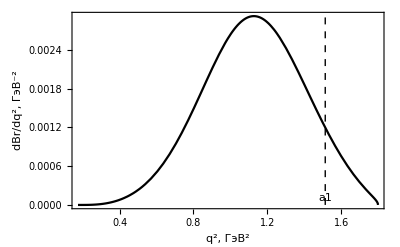
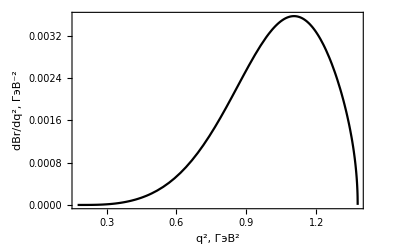
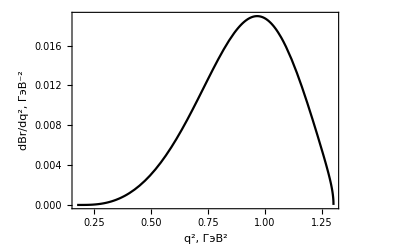
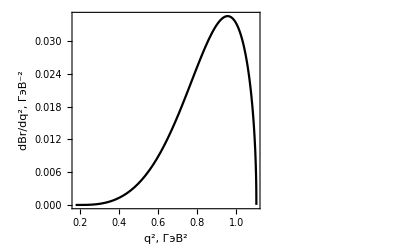
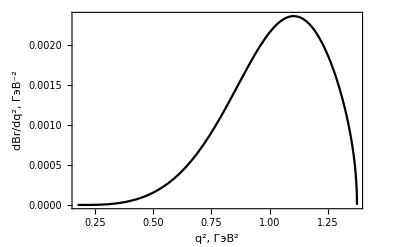
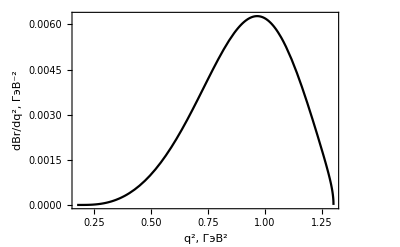
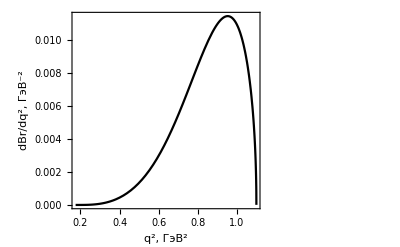
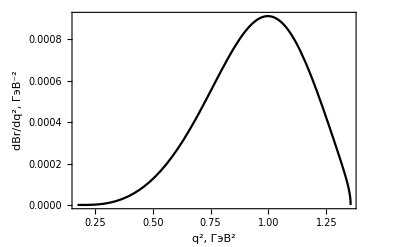
(in | out | l nul | pi | rho | 2 pi | 3 pi | 4 pi | 5 pi | Γπ/Γπ0 | Γρ/Γρ0 | Γa1/Γa10 | plot
\Xi_{cc}^{++} | \Lambda_{c}^{+} | 0.4936 | 0.403775 | 1.06272 | 0.8646 | 0.20393 | 0.04814 | 0.00027 | 0.986105 | 0.986473 | 0.986978 | -Graphics-
\Xi_{cc}^{++} | \Sigma_{c}^{+} | 0.4503 | 0.261326 | 1.12264 | 0.90497 | 0.18642 | 0.02255 | 0.00009 | 0.985836 | 0.981994 | 0 | -Graphics-
\Xi_{cc}^{++} | \Xi_{c}^{+} | 4.9858 | 6.87079 | 13.1897 | 10.171 | 0.98917 | 0.09019 | 0.00039 | 0.946025 | 0.931464 | 0 | -Graphics-
\Xi_{cc}^{++} | \Xi_{c}^{\prime+} | 5.975 | 4.98482 | 18.8378 | 14.255 | 1.31453 | 0.10158 | 0.00056 | 0.986338 | 0.982763 | 0 | -Graphics-
\Xi_{cc}^{+} | \Sigma_{c}^{0} | 0.2988 | 0.173802 | 0.746346 | 0.60138 | 0.12326 | 0.01483 | 0.00006 | 0.98717 | 0.981516 | 0 | -Graphics-
\Xi_{cc}^{+} | \Xi_{c}^{0} | 1.6513 | 2.27555 | 4.36833 | 3.36855 | 0.32761 | 0.02987 | 0.00013 | 0.952013 | 0.940566 | 0 | -Graphics-
\Xi_{cc}^{+} | \Xi_{c}^{\prime0} | 1.984 | 1.65914 | 6.26551 | 4.73854 | 0.43377 | 0.03345 | 0.00019 | 0.98396 | 0.98673 | 0 | -Graphics-
\Omega_{cc}^{+} | \Xi_{c}^{0} | 0.2079 | 0.254662 | 0.547982 | 0.42522 | 0.04921 | 0.00491 | 0.00002 | 0.955056 | 0.942158 | 0 | -Graphics-
\Omega_{cc}^{+} | \Xi_{c}^{\prime0} | 0.2492 | 0.184516 | 0.760756 | 0.58352 | 0.06489 | 0.0053 | 0.00003 | 0.986414 | 0.986453 | 0 | -Graphics-
\Omega_{cc}^{+} | \Omega_{c}^{0} | 6.6604 | 6.95065 | 24.1357 | 17.1055 | 0.73517 | 0.05073 | 0.00021 | 0.984442 | 0.994868 | 0 | -Graphics-
\Xi_{bb}^{0} | \Sigma_{b}^{+} | 0.0043 | 0.00014267 | 0.000464 | 0.00048 | 0.00025 | 0.00039 | 0.00013 | 0.979084 | 0.977039 | 0.982375 | -Graphics-
\Xi_{bb}^{0} | \Xi_{bc}^{+} | 2.5911 | 0.209334 | 0.607478 | 0.57727 | 0.27212 | 0.37447 | 0.08798 | 0.98571 | 0.982966 | 0.983024 | -Graphics-
\Xi_{bb}^{0} | \Xi_{bc}^{\prime+} | 1.1503 | 0.0414722 | 0.136714 | 0.14087 | 0.0734 | 0.114 | 0.03877 | 0.984847 | 0.981851 | 0.985905 | -Graphics-
\Xi_{bb}^{-} | \Lambda_{b}^{0} | 0.0011 | 0.0000794 | 0.000238 | 0.00023 | 0.00012 | 0.00016 | 0.00004 | 0.120858 | 0.125591 | 0.131601 | -Graphics-
\Xi_{bb}^{-} | \Sigma_{b}^{0} | 0.0022 | 0.00007151 | 0.000233 | 0.00024 | 0.00013 | 0.0002 | 0.00007 | 0.984224 | 0.977164 | 0.9821 | -Graphics-
\Xi_{bb}^{-} | \Xi_{bc}^{0} | 2.6207 | 0.210862 | 0.611952 | 0.58164 | 0.27418 | 0.37738 | 0.08886 | 2.46072 | 2.30954 | 2.11709 | -Graphics-
\Xi_{bb}^{-} | \Xi_{bc}^{\prime0} | 1.1556 | 0.0414366 | 0.136589 | 0.14079 | 0.07334 | 0.11393 | 0.03885 | 0.690194 | 0.735454 | 0.792965 | -Graphics-
\Omega_{bb}^{-} | \Xi_{b}^{0} | 0.002 | 0.00016106 | 0.000483 | 0.00046 | 0.00023 | 0.00032 | 0.00007 | 0.116003 | 0.119653 | 0.125686 | -Graphics-
\Omega_{bb}^{-} | \Xi_{b}^{\prime0} | 0.0044 | 0.00014898 | 0.000485 | 0.0005 | 0.00026 | 0.00041 | 0.00013 | 0.0600632 | 0.0676203 | 0.0797354 | -Graphics-
\Omega_{bb}^{-} | \Omega_{bc}^{0} | 4.8074 | 0.418442 | 1.21312 | 1.14873 | 0.54162 | 0.74262 | 0.16723 | 0.974325 | 0.977569 | 0.97872 | -Graphics-
\Omega_{bb}^{-} | \Omega_{bc}^{\prime0} | 2.1266 | 0.0827454 | 0.274009 | 0.28109 | 0.14756 | 0.2292 | 0.07469 | 0.984256 | 0.982069 | 0.985066 | -Graphics-
\Xi_{bc}^{+} | \Lambda_{b}^{0} | 0.2234 | 0.196761 | 0.520106 | 0.41699 | 0.08356 | 0.01497 | 0.00007 | 0.983643 | 0.988769 | 0.992814 | -Graphics-
\Xi_{bc}^{+} | \Sigma_{b}^{0} | 0.1483 | 0.104319 | 0.430935 | 0.33489 | 0.04437 | 0.00394 | 0.00002 | 0.985814 | 0.987025 | 0 | -Graphics-
\Xi_{bc}^{+} | \Xi_{b}^{0} | 2.3 | 3.21002 | 6.24725 | 4.7785 | 0.41419 | 0.03542 | 0.00017 | 0.986669 | 1.00241 | 0 | -Graphics-
\Xi_{bc}^{0} | \Sigma_{b}^{-} | 0.1121 | 0.0792393 | 0.326911 | 0.25379 | 0.03319 | 0.00293 | 0.00002 | 0.986015 | 0.984954 | 0 | -Graphics-
\Xi_{bc}^{0} | \Xi_{b}^{-} | 0.8684 | 1.21785 | 2.36073 | 1.8048 | 0.15463 | 0.01315 | 0.00007 | 0.986329 | 0.999471 | 0 | -Graphics-
\Omega_{bc}^{0} | \Xi_{b}^{-} | 0.2542 | 0.197056 | 0.546928 | 0.44383 | 0.10359 | 0.02381 | 0.00013 | 0.984637 | 0.990453 | 0.986769 | -Graphics-
\Omega_{bc}^{0} | \Omega_{b}^{-} | 6.0272 | 4.51047 | 17.7668 | 13.7286 | 1.67943 | 0.14397 | 0.00071 | 0.982206 | 0.985208 | 0 | -Graphics-
\Xi_{bc}^{+} | \Sigma_{c}^{++} | 0.0035 | 0.00008039 | 0.000254 | 0.00027 | 0.00014 | 0.00021 | 0.00009 | 0.983928 | 0.980373 | 0.985281 | -Graphics-
\Xi_{bc}^{+} | \Xi_{cc}^{++} | 1.5843 | 0.165958 | 0.468397 | 0.43695 | 0.20011 | 0.26547 | 0.05444 | 0.985446 | 0.984319 | 0.986825 | -Graphics-
\Xi_{bc}^{0} | \Lambda_{c}^{+} | 0.0003 | 0.00001553 | 0.000046 | 0.00005 | 0.00003 | 0.00003 | 0.00001 | 0.989636 | 0.984904 | 0.987827 | -Graphics-
\Xi_{bc}^{0} | \Sigma_{c}^{+} | 0.0007 | 0.00001532 | 0.000049 | 0.00006 | 0.00003 | 0.00004 | 0.00002 | 0.984275 | 0.979305 | 0.983713 | -Graphics-
\Xi_{bc}^{0} | \Xi_{cc}^{+} | 0.6027 | 0.0631272 | 0.178169 | 0.16621 | 0.07612 | 0.10098 | 0.02071 | 0.985446 | 0.984319 | 0.986825 | -Graphics-
\Omega_{bc}^{0} | \Xi_{c}^{+} | 0.0005 | 0.00003206 | 0.000095 | 0.0001 | 0.00005 | 0.00006 | 0.00002 | 0.974472 | 0.971157 | 0.973939 | -Graphics-
\Omega_{bc}^{0} | \Omega_{cc}^{+} | 1.8684 | 0.161638 | 0.459336 | 0.43253 | 0.1991 | 0.26769 | 0.06104 | 0.985845 | 0.982536 | 0.986564 | -Graphics-)

```mathematica
result1={};
AppendTo[result1,{"in","out","l nul","pi" ,"rho","2 pi","3 pi","4 pi","5 pi", "Γπ/Γπ0", "Γρ/Γρ0", "Γa1/Γa10", "plot"}];
i=.0;
PrintTemporary[Dynamic[dec],"Завершено",Dynamic[Floor[i/36*100,-0.1]], "%" ];
Do[
{in,out}=dec;
i=i+1;
Clear[m1,m2,quark1,quark2,f1,f2,g1,g2,Vckm,cS,cA];
m1=dsParticles[in]["mass"]; m2=dsParticles[out]["mass"];
cA=cA1[out,in];cS=cS1[out,in];
f1=FF[Select[#in==in&&#out==out&&#f=="f1"&]];
f2=FF[Select[#in==in&&#out==out&&#f=="f2"&]];
g1=FF[Select[#in==in&&#out==out&&#f=="g1"&]];
g2=FF[Select[#in==in&&#out==out&&#f=="g2"&]];
quark1=Characters[Quarks[in]];
quark2=Characters[Quarks[out]];
Vckm1=First[(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]])];
quarkrazn=(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]]);
Vckm2=-quarkrazn+Vckm1;
Vckm=V[Vckm1,Vckm2];
m3=0; m4=0;
Γl1=NIntegrate[dΓl, {m232,0,(m1-m2)^2}];
Γl2=NIntegrate[dΓl1,{m122,m12min,m12max},{m232,m23min,m23max}];
Γl0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\nu"]&]][[1]]["width"];
Brl=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\nu"]&]][[1]]["br"];
fullΓ=Γl0/Brl;
Hρ=HT/.{m232-> mρ^2};
Γρ=(Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*fρ^2*(1/(8*π))*a1*Vckm^2*Hρ;
Ha1=HT/.{m232-> ma1^2};
Γa1=(Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*fa1^2*(1/(8*π))*a1*Vckm^2*Ha1;
Hπ=HL/.{m232-> mπ^2};
Γπ=(Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*fπ^2*(1/(8*π))*a1*Vckm^2*Hπ;
Γρ0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\rho"]&]][[1]]["width"];
Γπ0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\pi"]&]][[1]]["width"];
Γa10=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"a_{1}"]&]][[1]]["width"];
Γ2π=NIntegrate[dΓ2π, {m232,4mπ^2,(m1-m2)^2}];
Γ3π=NIntegrate[dΓ3π, {m232,9mπ^2,(m1-m2)^2}];
Γ4π=NIntegrate[dΓ4π, {m232,16mπ^2,(m1-m2)^2}];
Γ5π=NIntegrate[dΓ5π, {m232,25mπ^2,(m1-m2)^2}];
Pic3π=dΓ3π/fullΓ;
plot111=Plot[Pic3π,{m232,9mπ^2,(m1-m2)^2}, Epilog-> {Text["a1",{ma1^2,0.0001}],Dashed,Line[{{ma1^2,0},{ma1^2,0.003}}]},FrameLabel->{"q^2, (:0413:044d:0412)^2","dBr/dq^2, (:0413:044d:0412)^-2"}, Frame-> True,PlotStyle->{Black} ];
AppendTo[result1,{in,out,Floor[Chop[Γl1/fullΓ],-0.000001]*100,Floor[Chop[Γπ/fullΓ],-0.0000000001]*100,Floor[Chop[Γρ/fullΓ],-0.00000001]*100,Floor[Chop[Γ2π/fullΓ],-0.0000001]*100,Floor[Chop[Γ3π/fullΓ],-0.0000001]*100,Floor[Chop[Γ4π/fullΓ],-0.0000001]*100,Floor[Chop[Γ5π/fullΓ],-0.0000001]*100, Chop[Γπ/Γπ0], Chop[Γρ/Γρ0], Chop[(Γa1/Γa10)], plot111}];
,{dec,decays}];
result1
```

Making TEX tables

```mathematica
dec1=Select[result,!StringFreeQ[#[[1]],"{cc}"]&];
dec2=Select[result,!StringFreeQ[#[[1]],"{bc}"]&];
dec3=Select[result,!StringFreeQ[#[[1]],"{bb}"]&];
```

```mathematica
toString[a_]:=If[Abs[a]<10^-3,ToString[ScientificForm[a,3],TeXForm],ToString[NumberForm[a,3]]];
makestr[dec_]:=Module[{str,qwert,in,out,Brlnul,Brπ,Brρ,Br2π, Br3π,Bra1,Br4π,Br5π},
str="\\begin{tabular}{|l|c|c|c|c|c|c|c|c|}\n";
str = str<>"\\hline \n";
str=str<>"\\multirow{2}{*}{$\\B_1\\to\ \\B_2$}& \\multicolumn{8}{c|}{Modes}"<>"\\\\"<>"\n";
str=str<>"\\cline{2-9}"<>"\n";
str=str<>"& $l\\nu_l$ & $\\pi$ & $\\rho$ & $2\\pi$ & $3\\pi$ &  $a_1$ & $4\\pi$ & $5\\pi$"<>"\\\\"<>"\n";
     str = str<>"\\hline \n"; 
str = str<>"\\hline \n";
Do[
{in,out,Brlnul,Brπ,Brρ,Br2π,Br3π,Bra1,Br4π,Br5π}=qwert;
str=str<>"$"<>in<>"\\to\ "<>out<>"$&$"<>toString[Brlnul]<>"$&$"<>toString[ Brπ]<>"$&$"<>toString[Brρ]<>"$&$"<>toString[Br2π ]<>"$&$"<>toString[Br3π ]<>"$&$"<>toString[Bra1]<>"$&$"<>toString[Br4π ]<>"$&$"<>toString[Br5π]<>"$\\\\"<>"\n";
str = str<>"\\hline \n";

,{qwert,dec}];
str=str<>"\\end{tabular}\n";
Return[str];
]
```

```mathematica
str1=makestr[dec1];
str2=makestr[dec2];
str3=makestr[dec3];
```

```mathematica
DeleteFile["table11.tex"];
DeleteFile["table22.tex"];
DeleteFile["table33.tex"];
WriteString["table11.tex",str1];
WriteString["table22.tex",str2];
WriteString["table33.tex",str3];
Close["table11.tex"];
Close["table22.tex"];
Close["table33.tex"];
```

# Pictures 3pi 5pi

```mathematica
in="\\Xi_{cc}^{++}";
out="\\Lambda_{c}^{+}";
in2=in;out2=out;
Clear[m1,m2,quark1,quark2,f1,f2,g1,g2,Vckm,cS,cA];
m1=dsParticles[in]["mass"]; m2=dsParticles[out]["mass"];
cA=cA1[out,in];cS=cS1[out,in];
f1=FF[Select[#in==in&&#out==out&&#f=="f1"&]];
f2=FF[Select[#in==in&&#out==out&&#f=="f2"&]];
g1=FF[Select[#in==in&&#out==out&&#f=="g1"&]];
g2=FF[Select[#in==in&&#out==out&&#f=="g2"&]];
quark1=Characters[Quarks[in]];
quark2=Characters[Quarks[out]];
Vckm1=First[(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]])];
quarkrazn=(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]]);
Vckm2=-quarkrazn+Vckm1;
Vckm=V[Vckm1,Vckm2];

Γl0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\nu"]&]][[1]]["width"];
Brl=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\nu"]&]][[1]]["br"];
fullΓ=Γl0/Brl;
Γ3π=NIntegrate[dΓ3π, {m232,9mπ^2,(m1-m2)^2}];
Γ5π=NIntegrate[dΓ5π, {m232,25mπ^2,(m1-m2)^2}];
pic2π=dΓ2π/fullΓ;
Pic3π=dΓ3π/fullΓ;
Pic5π=dΓ5π/fullΓ;
```

```mathematica
qqq=ma1^2
```

1.5129

```mathematica
qqq=1
```

1

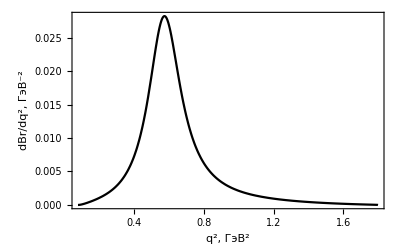

```mathematica
plot2π=Plot[pic2π,{m232,4mπ^2,(m1-m2)^2}, FrameLabel->{"q^2, (:0413:044d:0412)^2","dBr/dq^2, (:0413:044d:0412)^-2"}, Frame-> True,PlotStyle->{Black} , PlotRangePadding-> 0]
```

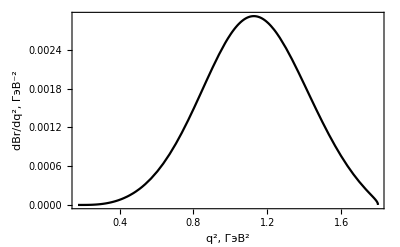

```mathematica
plot3π=Plot[Pic3π,{m232,9mπ^2,(m1-m2)^2}, FrameLabel->{"q^2, (:0413:044d:0412)^2","dBr/dq^2, (:0413:044d:0412)^-2"}, Frame-> True,PlotStyle->{Black} , PlotRangePadding-> 0]
```

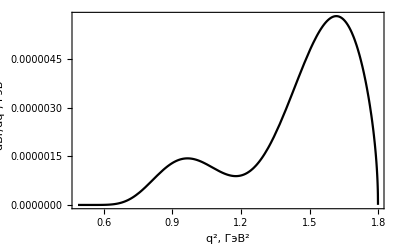

```mathematica
plot5π=Plot[Pic5π,{m232,25mπ^2,(m1-m2)^2},FrameLabel->{"q^2, (:0413:044d:0412)^2","dBr/dq^2, (:0413:044d:0412)^-2"}, Frame-> True,PlotStyle->{Black},  PlotRangePadding-> 0 ]
```

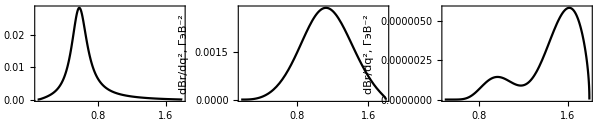

General::openx: pic3pi5pi.eps is not open.

```mathematica
Delete["pic3pi5pi.eps"];
GraphicsGrid[{{plot2π,plot3π,plot5π}},ImageSize-> 600, Spacings->20]
Export["pic3pi5pi.eps",%];
Close["pic3pi5pi.eps"];
```

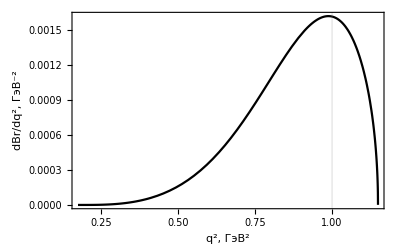
-Graphics-text

```mathematica
plot3=Labeled[Plot[Pic3π,{m232,9mπ^2,(m1-m2)^2}, GridLines->{{qqq},{}},FrameLabel->{"q^2, (:0413:044d:0412)^2","dBr/dq^2, (:0413:044d:0412)^-2"}, Frame-> True,PlotStyle->{Black} ],"text"]
```

# Pics l nul

```mathematica
in="\\Omega_{cc}^{+}";
out="\\Xi_{c}^{\\prime0}";
in2=in;out2=out;
Clear[m1,m2,quark1,quark2,f1,f2,g1,g2,Vckm,cS,cA];
m1=dsParticles[in]["mass"]; m2=dsParticles[out]["mass"];
cA=cA1[out,in];cS=cS1[out,in];
f1=FF[Select[#in==in&&#out==out&&#f=="f1"&]];
f2=FF[Select[#in==in&&#out==out&&#f=="f2"&]];
g1=FF[Select[#in==in&&#out==out&&#f=="g1"&]];
g2=FF[Select[#in==in&&#out==out&&#f=="g2"&]];
quark1=Characters[Quarks[in]];
quark2=Characters[Quarks[out]];
Vckm1=First[(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]])];
quarkrazn=(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]]);
Vckm2=-quarkrazn+Vckm1;
Vckm=V[Vckm1,Vckm2];
m3=0;m4=0;
Γl1=NIntegrate[dΓl, {m232,0,(m1-m2)^2}];
Γl2=NIntegrate[dΓl1,{m122,m12min,m12max},{m232,m23min,m23max}];
Γl0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\nu"]&]][[1]]["width"];
Brl=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\nu"]&]][[1]]["br"];
fullΓ=Γl0/Brl;
Γ2= Γl1;
dΓ2=dΓl;
mass2=m1-m2;
Γtab2=dΓl1/Γl0;
m23mintab2=m23min;
m23maxtab2=m23max;
m12mintab2=m12min;
m12maxtab2=m12max;
ΓΓ2=dΓ2/Γ2;
tab2=Table[
{m122, NIntegrate[Γtab2, {m232, m23mintab2, m23maxtab2}] }
,{m122, m12min, m12max, (m12max-m12min)/100}];
pic2π1=dΓ2π/fullΓ;
Pic3π1=dΓ3π/fullΓ;
Pic5π1=dΓ5π/fullΓ;
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m232 near {m232} = {4.44789×10^-16}. NIntegrate obtained -5.20253×10^-31 and 5.87168×10^-35 for the integral and error estimates.

```mathematica
in="\\Xi_{bb}^{-}";
out="\\Sigma_{b}^{0}";
in4=in;out4=out;
Clear[m1,m2,quark1,quark2,f1,f2,g1,g2,Vckm,cS,cA];
m1=dsParticles[in]["mass"]; m2=dsParticles[out]["mass"];
cA=cA1[out,in];cS=cS1[out,in];
f1=FF[Select[#in==in&&#out==out&&#f=="f1"&]];
f2=FF[Select[#in==in&&#out==out&&#f=="f2"&]];
g1=FF[Select[#in==in&&#out==out&&#f=="g1"&]];
g2=FF[Select[#in==in&&#out==out&&#f=="g2"&]];
quark1=Characters[Quarks[in]];
quark2=Characters[Quarks[out]];
Vckm1=First[(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]])];
quarkrazn=(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]]);
Vckm2=-quarkrazn+Vckm1;
Vckm=V[Vckm1,Vckm2];
m3=0;m4=0;
Γl1=NIntegrate[dΓl, {m232,0,(m1-m2)^2}];
Γl2=NIntegrate[dΓl1,{m122,m12min,m12max},{m232,m23min,m23max}];
Γl0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\nu"]&]][[1]]["width"];
Brl=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\nu"]&]][[1]]["br"];
fullΓ=Γl0/Brl;
Γ4= Γl1;
dΓ4=dΓl;
mass4=m1-m2;
Γtab4=dΓl1/Γl0;
ΓΓ4=dΓ4/Γ4;
tab4=Table[
{m122, NIntegrate[Γtab4, {m232, m23min, m23max}] }
,{m122, m12min, m12max, (m12max-m12min)/100}];
pic2π2=dΓ2π/fullΓ;
Pic3π2=dΓ3π/fullΓ;
Pic5π2=dΓ5π/fullΓ;
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m232 near {m232} = {-6.07858×10^-15}. NIntegrate obtained -2.78088×10^-32 and 3.80529×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m232 near {m232} = {3.56104×10^-15}. NIntegrate obtained -4.59635×10^-34 and 1.39985×10^-35 for the integral and error estimates.

```mathematica
in="\\Xi_{cc}^{++}";
out="\\Xi_{c}^{+}";
in5=in;out5=out;
Clear[m1,m2,quark1,quark2,f1,f2,g1,g2,Vckm,cS,cA];
m1=dsParticles[in]["mass"]; m2=dsParticles[out]["mass"];
cA=cA1[out,in];cS=cS1[out,in];
f1=FF[Select[#in==in&&#out==out&&#f=="f1"&]];
f2=FF[Select[#in==in&&#out==out&&#f=="f2"&]];
g1=FF[Select[#in==in&&#out==out&&#f=="g1"&]];
g2=FF[Select[#in==in&&#out==out&&#f=="g2"&]];
quark1=Characters[Quarks[in]];
quark2=Characters[Quarks[out]];
Vckm1=First[(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]])];
quarkrazn=(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]]);
Vckm2=-quarkrazn+Vckm1;
Vckm=V[Vckm1,Vckm2];
m3=0;m4=0;
Γl1=NIntegrate[dΓl, {m232,0,(m1-m2)^2}];
Γl2=NIntegrate[dΓl1,{m122,m12min,m12max},{m232,m23min,m23max}];
Γl0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\nu"]&]][[1]]["width"];
Brl=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\nu"]&]][[1]]["br"];
fullΓ=Γl0/Brl;
Γ5= Γl1;
dΓ5=dΓl;
mass5=m1-m2;
Γtab5=dΓl1/Γl0;
m23mintab5=m23min;
m23maxtab5=m23max;
m12mintab5=m12min;
m12maxtab5=m12max;
ΓΓ5=dΓ5/Γ5;
tab5=Table[
{m122, NIntegrate[Γtab5, {m232, m23min, m23max}] }
,{m122, m12min, m12max, (m12max-m12min)/100}];
pic2π3=dΓ2π/fullΓ;
Pic3π3=dΓ3π/fullΓ;
Pic5π3=dΓ5π/fullΓ;
```

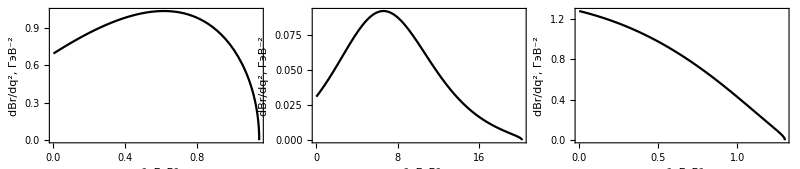

General::openx: lnul.eps is not open.

```mathematica
Delete["lnul.eps"];
GraphicsGrid[{{Plot[ΓΓ2,{m232,0,mass2^2},PlotStyle->Black,FrameLabel->{"q^2, (:0413:044d:0412)^2","dBr/dq^2, (:0413:044d:0412)^-2"}, Frame-> True,   PlotRangePadding-> 0 ],Plot[ΓΓ4,{m232,0,mass4^2},PlotStyle->Black,FrameLabel->{"q^2, (:0413:044d:0412)^2","dBr/dq^2, (:0413:044d:0412)^-2"}, Frame-> True,   PlotRangePadding-> 0 ],Plot[ΓΓ5,{m232,0,mass5^2},PlotStyle->Black,FrameLabel->{"q^2, (:0413:044d:0412)^2","dBr/dq^2, (:0413:044d:0412)^-2"}, Frame-> True,   PlotRangePadding-> 0 ]}},ImageSize-> 800, Spacings->-15]
Export["lnul.eps",%];
Close["lnul.eps"];
```

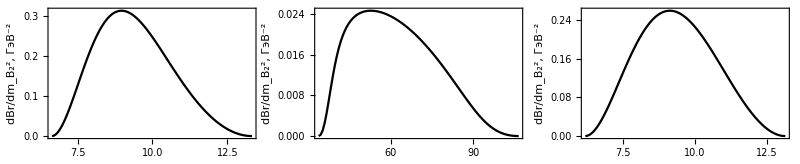

General::openx: lnul2.eps is not open.

```mathematica
Delete["lnul2.eps"];
GraphicsGrid[{{ListPlot[tab2,Joined->True,PlotStyle->Black, FrameLabel->{"m_B_2^2, (:0413:044d:0412)^2","dBr/dm_B_2^2, (:0413:044d:0412)^-2"}, Frame-> True,  PlotRangePadding-> 0 ],ListPlot[tab4,Joined->True,PlotStyle->Black, FrameLabel->{"m_B_2^2, (:0413:044d:0412)^2","dBr/dm_B_2^2, (:0413:044d:0412)^-2"}, Frame-> True,  PlotRangePadding-> 0 ],ListPlot[tab5,Joined->True,PlotStyle->Black, FrameLabel->{"m_B_2^2, (:0413:044d:0412)^2","dBr/dm_B_2^2, (:0413:044d:0412)^-2"}, Frame-> True,  PlotRangePadding-> 0 ]}}, ImageSize-> 800, Spacings->0]
Export["lnul2.eps",%];
Close["lnul2.eps"];
```

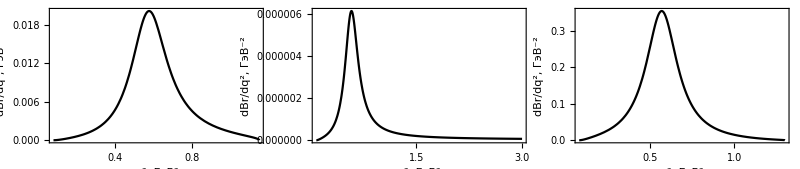

```mathematica
GraphicsGrid[{{Plot[pic2π1,{m232,4mπ^2,mass2^2},PlotStyle->Black,FrameLabel->{"q^2, (:0413:044d:0412)^2","dBr/dq^2, (:0413:044d:0412)^-2"}, Frame-> True,   PlotRangePadding-> 0 ],Plot[pic2π2,{m232,4mπ^2,3},PlotStyle->Black,FrameLabel->{"q^2, (:0413:044d:0412)^2","dBr/dq^2, (:0413:044d:0412)^-2"}, Frame-> True,   PlotRangePadding-> 0 , PlotRange->All],Plot[pic2π3,{m232,4mπ^2,mass5^2},PlotStyle->Black,FrameLabel->{"q^2, (:0413:044d:0412)^2","dBr/dq^2, (:0413:044d:0412)^-2"}, Frame-> True,   PlotRangePadding-> 0 ]}},ImageSize-> 800, Spacings->-15]
```

# H_T H_L

```mathematica
Clear[m232,q,m1,m2,m3,m4, Fq3π,Fq5π,Vckm,f1,f2,g1,g2];
www=HT/λ
qqq=HL/λ
```

1/m1^2 2 (f1^2 m1^2 (m1^4+m1^2 (m232-2 m2^2)-6 m1 m2 m232+m2^4+m2^2 m232-2 m232^2)-6 f1 f2 m1 m232 (m1+m2) (m1^2-2 m1 m2+m2^2-m232)-m232 (f2^2 (-2 m1^4+m1^2 (4 m2^2+m232)+6 m1 m2 m232-2 m2^4+m2^2 m232+m232^2)+g2^2 (-2 m1^4+m1^2 (4 m2^2+m232)-6 m1 m2 m232-2 m2^4+m2^2 m232+m232^2))+g1^2 m1^2 (m1^4+m1^2 (m232-2 m2^2)+6 m1 m2 m232+m2^4+m2^2 m232-2 m232^2)+6 g1 g2 m1 m232 (m1-m2) (m1^2+2 m1 m2+m2^2-m232))

f1^2 (m232 (-2. m1^2+4. m1 m2-2. m2^2-7.10543×10^-15)+73.4345)+(f1 f2 (4. m1^3 m232-4. m1^2 m2 m232+m1 ((-4. m2^2-24.2379) m232-2.84217×10^-13)+m2 ((4. m2^2+24.2379) m232-1.13687×10^-13)))/m1+(f2^2 (-2. m1^4 m232+m1^2 ((4. m2^2+24.2379) m232+1.7053×10^-13)+m1 m2 (2.27374×10^-13-1.42109×10^-14 m232)-2. m2^4 m232+m2^2 (2.84217×10^-14-24.2379 m232)-73.4345 m232))/m1^2-2. g1^2 m1^2 m232-4. g1^2 m1 m2 m232-2. g1^2 m2^2 m232-7.10543×10^-15 g1^2 m232+73.4345 g1^2-4. g1 g2 m1^2 m232+(4. g1 g2 m2^3 m232)/m1-4. g1 g2 m1 m2 m232+(24.2379 g1 g2 m2 m232)/m1-(1.13687×10^-13 g1 g2 m2)/m1+4. g1 g2 m2^2 m232+24.2379 g1 g2 m232+2.84217×10^-13 g1 g2-(2. g2^2 m2^4 m232)/m1^2-(24.2379 g2^2 m2^2 m232)/m1^2+(2.84217×10^-14 g2^2 m2^2)/m1^2-2. g2^2 m1^2 m232-(73.4345 g2^2 m232)/m1^2+(1.42109×10^-14 g2^2 m2 m232)/m1-(2.27374×10^-13 g2^2 m2)/m1+4. g2^2 m2^2 m232+24.2379 g2^2 m232+1.7053×10^-13 g2^2

```mathematica
StringReplace[StringReplace[ToString[Simplify[m1^2 qqq,m1==(Mplus+Mminus)/2&&m2==(Mplus-Mminus)/2],TeXForm],{"\\text{f1}"->"f_1","\\text{f2}"->"f_2","\\text{g1}"->"g_1","\\text{g2}"->"g_2","\\text{Mplus}"->"M_{+}","\\text{Mminus}"->"M_{-}","\\text{m232}"->"q^2","\\left"->"","\\right"->""}],{"q^2^2"->"q^4"}]
```

f_1^2 \text{m1}^2 (q^2 (-2. M_{-}^2-\text{7.105427357601002$\grave{ }$*${}^{\wedge}$-15})+73.4345)+f_1 f_2 (2. q^2 M_{-}^3 M_{+}+M_{-}^2 (2. q^2 M_{+}^2-12.119 q^2-\text{4.263256414560601$\grave{ }$*${}^{\wedge}$-14})+(-12.119 q^2-\text{1.4210854715202004$\grave{ }$*${}^{\wedge}$-13}) M_{-} M_{+}-\text{9.947598300641403$\grave{ }$*${}^{\wedge}$-14} M_{+}^2)-2. f_2^2 q^2 M_{-}^2 M_{+}^2+\text{3.552713678800501$\grave{ }$*${}^{\wedge}$-15} f_2^2 q^2 M_{-}^2+24.2379 f_2^2 q^2 M_{-} M_{+}-\text{3.552713678800501$\grave{ }$*${}^{\wedge}$-15} f_2^2 q^2 M_{+}^2-73.4345 f_2^2 q^2-\text{7.105427357601002$\grave{ }$*${}^{\wedge}$-15} f_2^2 M_{-}^2+\text{7.105427357601002$\grave{ }$*${}^{\wedge}$-14} f_2^2 M_{-} M_{+}+\text{1.0658141036401503$\grave{ }$*${}^{\wedge}$-13} f_2^2 M_{+}^2+g_1^2 \text{m1}^2 (q^2 (-2. M_{+}^2-\text{7.105427357601002$\grave{ }$*${}^{\wedge}$-15})+73.4345)+g_1 g_2 (M_{-}^2 (\text{9.947598300641403$\grave{ }$*${}^{\wedge}$-14}-2. q^2 M_{+}^2)+M_{-} M_{+} (-2. q^2 M_{+}^2+12.119 q^2+\text{1.4210854715202004$\grave{ }$*${}^{\wedge}$-13})+(12.119 q^2+\text{4.263256414560601$\grave{ }$*${}^{\wedge}$-14}) M_{+}^2)-2. g_2^2 q^2 M_{-}^2 M_{+}^2-\text{3.552713678800501$\grave{ }$*${}^{\wedge}$-15} g_2^2 q^2 M_{-}^2+24.2379 g_2^2 q^2 M_{-} M_{+}+\text{3.552713678800501$\grave{ }$*${}^{\wedge}$-15} g_2^2 q^2 M_{+}^2-73.4345 g_2^2 q^2+\text{1.0658141036401503$\grave{ }$*${}^{\wedge}$-13} g_2^2 M_{-}^2+\text{7.105427357601002$\grave{ }$*${}^{\wedge}$-14} g_2^2 M_{-} M_{+}-\text{7.105427357601002$\grave{ }$*${}^{\wedge}$-15} g_2^2 M_{+}^2

# Formfactors tables

```mathematica
Clear[str];
str="\\begin{table}\n";
str=str<>"\\begin{center}\n";
str=str<>"\\begin{tabular}{|l|c|c|c|c|c|}\n";
str = str<>"\\hline \n";
str=str<>"\multirow{2}{*}{$\\B_1\\to\ \\B_2$}& \multicolumn{5}{c|}{Modes}"<>"\\\\"<>"\n";
str=str<>"\cline{2-6}"<>"\n";
str=str<>"& $l\\nu_l$ & $\\rho$ & $\\pi$ & $3\\pi$ & $5\\pi$"<>"\\\\"<>"\n";
str = str<>"\\hline \n";
Clear[t];
For[i=2,i≤11,i++,
{in,out,Brlnul,Brρ,Brπ,Br3π,Br5π}=result[[i]];

str=str<>"$"<>in<>"\\to\ "<>out<>"$&$"<>ToString[TeXForm[ScientificForm[ Chop[Brlnul],3]]]<>"$&$"<>ToString[TeXForm[ScientificForm[ Brρ,3]]]<>"$&$"<>ToString[TeXForm[ScientificForm[Brπ,3]]]<>"$&$"<>ToString[TeXForm[ScientificForm[Br3π ,3]]]<>"$&$"<>ToString[TeXForm[ScientificForm[Br5π,3]]]<>"$\\\\"<>"\n";
str = str<>"\\hline \n";
]
str=str<>"\\end{tabular}\n";
str=str<>"\\caption{Относительные вероятности распадов дважды очарованных барионов)}\n";
str=str<>"\\label{results}\n";
str=str<>"\\end{center}\n";
str=str<>"\\end{table}\n";
str1=str;
str1
```

# Pictures of spec fucs

```mathematica
Fq3π
```

(0.000039307 (m232-0.17532)^4 (190 m232+1))/(((m232-1.06)^2+0.48)^2 m232^4)

```mathematica
Fq5π
```

(27.67 (m232-0.486999)^10 (0.69 m232^2-1.65 m232+1))/(m232^10 ((m232+2.21)^2-4.69)^3)

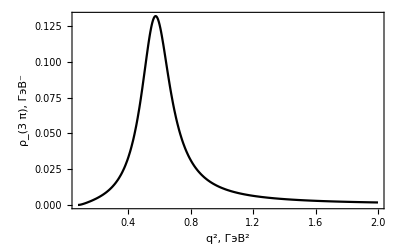

```mathematica
spec2π=Plot[Fq2π,{m232,4mπ^2,2}, FrameLabel->{"q^2, (:0413:044d:0412)^2","ρ_(3  π), (:0413:044d:0412)^-"}, Frame-> True,PlotStyle->{Black}, PlotRangePadding-> 0 ]
```

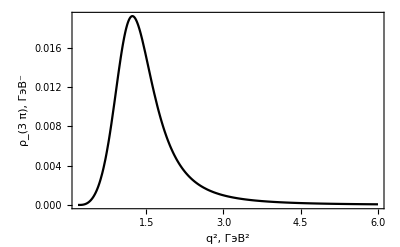

```mathematica
spec3π=Plot[Fq3π,{m232,9mπ^2,6}, FrameLabel->{"q^2, (:0413:044d:0412)^2","ρ_(3  π), (:0413:044d:0412)^-"}, Frame-> True,PlotStyle->{Black}, PlotRangePadding-> 0 ]
```

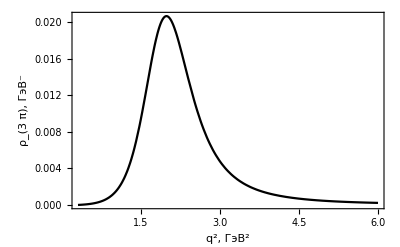

```mathematica
spec4π=Plot[Fq4π,{m232,16mπ^2,6}, FrameLabel->{"q^2, (:0413:044d:0412)^2","ρ_(3  π), (:0413:044d:0412)^-"}, Frame-> True,PlotStyle->{Black} , PlotRangePadding-> 0]
```

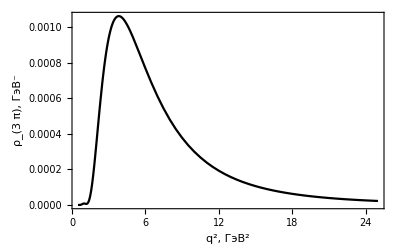

```mathematica
spec5π=Plot[Fq5π,{m232,25mπ^2,25}, FrameLabel->{"q^2, (:0413:044d:0412)^2","ρ_(3  π), (:0413:044d:0412)^-"}, Frame-> True,PlotStyle->{Black} , PlotRangePadding-> 0]
```

```mathematica
Delete["spec2pi.eps"];
Export["spec2pi.eps", spec2π];
Close["spec2pi.eps"];
Delete["spec3pi.eps"];
Export["spec3pi.eps", spec3π];
Close["spec3pi.eps"];
Delete["spec4pi.eps"];
Export["spec4pi.eps", spec4π];
Close["spec4pi.eps"];
Delete["spec5pi.eps"];
Export["spec5pi.eps", spec5π];
Close["spec5pi.eps"];
```

General::openx: spec2pi.eps is not open.

General::openx: spec3pi.eps is not open.

General::openx: spec4pi.eps is not open.

General::openx: spec5pi.eps is not open.